```mathematica
dx1=0;
dx2=0;
dx3=0;

ds1=0;
ds2=0;
ds3=0;

h1=0.19;
h2=0.23;
h3=0.39;

X[1]=-1/2+dx2+dx1;
X[2]=1-dx1;
X[3]=-1/2-dx2;
X[4]=-1/2-dx3;
X[5]=1+dx2+dx3;
X[6]=-1/2-dx1+dx3;
X[7]=-1/2-dx3;
X[8]=-1/2-dx2;
X[9]=-1/2+dx2+dx1;
X[10]=1-dx2-dx3;
X[11]=-1/2-dx1+dx3;
X[12]=1+dx1;

Y[1]=-Sqrt[3]/2+ds1+ds2;
Y[2]=-ds1;
Y[3]=Sqrt[3]/2-ds2;
Y[4]=-Sqrt[3]/2-ds3;
Y[5]=ds2+ds3;
Y[6]=-Sqrt[3]/2-ds1+ds3;
Y[7]=Sqrt[3]/2-ds3;
Y[8]=-Sqrt[3]/2-ds2;
Y[9]=Sqrt[3]/2+ds2+ds1;
Y[10]=-ds2-ds3;
Y[11]=Sqrt[3]/2-ds1+ds3;
Y[12]=ds1;



Z[1]=h1+h2;
Z[2]=-h1;
Z[3]=-h2;
Z[4]=0-h3;
Z[5]=h2+h3;
Z[6]=-h1+h3;
Z[7]=0-h3;
Z[8]=-h2;
Z[9]=h1+h2;
Z[10]=-h2-h3;
Z[11]=-h1+h3;
Z[12]=h1;
For[i=1,i≤12,i++,S[i]=Sqrt[X[i]^2+Y[i]^2+Z[i]^2]];
For[i=1,i≤12,i++,VN[i]={X[i],Y[i],Z[i]}/S[i]];
For[i=1,i≤12,i++,VN1[i]={-Y[i],X[i],0}/Sqrt[X[i]^2+Y[i]^2]];
For[i=1,i≤12,i++,VN2[i]=Cross[VN[i],VN1[i]]];
Clear[S1,S2,kx,ky]
For[i=1,i≤12,i++,NSS[i]=-2S[i]VN[i]];
NDS[1]=S1[2]VN1[2]+S1[3]VN1[3]+S1[10]VN1[10]+S1[11]VN1[11]+S2[2]VN2[2]+S2[3]VN2[3]+S2[10]VN2[10]+S2[11]VN2[11];
NDS[2]=S1[1]VN1[1]+S1[3]VN1[3]+S1[8]VN1[8]Exp[-I ky Sqrt[3]/2]+S1[9]VN1[9]Exp[-I ky Sqrt[3]/2]+S2[1]VN2[1]+S2[3]VN2[3]+S2[8]VN2[8]Exp[-I ky Sqrt[3]/2]+S2[9]VN2[9]Exp[-I ky Sqrt[3]/2];
NDS[3]=S1[1]VN1[1]+S1[2]VN1[2]+S1[4]VN1[4]+S1[5]VN1[5]+S2[1]VN2[1]+S2[2]VN2[2]+S2[4]VN2[4]+S2[5]VN2[5];
NDS[4]=S1[3]VN1[3]+S1[5]VN1[5]+S1[11]VN1[11]Exp[I kx]+S1[12]VN1[12]Exp[I kx]+S2[3]VN2[3]+S2[5]VN2[5]+S2[11]VN2[11]Exp[I kx]+S2[12]VN2[12]Exp[I kx];
NDS[5]=S1[3]VN1[3]+S1[4]VN1[4]+S1[7]VN1[7]+S1[8]VN1[8]+S2[3]VN2[3]+S2[4]VN2[4]+S2[7]VN2[7]+S2[8]VN2[8];
NDS[6]=S1[7]VN1[7]+S1[9]VN1[9]Exp[I kx]+S1[10]VN1[10]Exp[I kx]+S1[12]VN1[12]Exp[I kx+I ky Sqrt[3]/2]+S2[7]VN2[7]+S2[9]VN2[9]Exp[I kx]+S2[10]VN2[10]Exp[I kx]+S2[12]VN2[12]Exp[I kx +I ky Sqrt[3]/2];
NDS[7]=S1[5]VN1[5]+S1[6]VN1[6]+S1[8]VN1[8]+S1[12]VN1[12]Exp[I kx+I ky Sqrt[3]/2]+S2[5]VN2[5]+S2[6]VN2[6]+S2[8]VN2[8]+S2[12]VN2[12]Exp[I kx+I ky Sqrt[3]/2];
NDS[8]=S1[5]VN1[5]+S1[7]VN1[7]+S1[9]VN1[9]+S1[2]VN1[2]Exp[I ky Sqrt[3]/2]+S2[5]VN2[5]+S2[7]VN2[7]+S2[9]VN2[9]+S2[2]VN2[2]Exp[I ky Sqrt[3]/2];
NDS[9]=S1[8]VN1[8]+S1[10]VN1[10]+S1[2]VN1[2]Exp[I ky Sqrt[3]/2]+S1[6]VN1[6]Exp[-I kx]+S2[8]VN2[8]+S2[10]VN2[10]+S2[2]VN2[2]Exp[I ky Sqrt[3]/2]+S2[6]VN2[6]Exp[-I kx];
NDS[10]=S1[1]VN1[1]+S1[9]VN1[9]+S1[11]VN1[11]+S1[6]VN1[6]Exp[-I kx]+S2[1]VN2[1]+S2[9]VN2[9]+S2[11]VN2[11]+S2[6]VN2[6]Exp[-I kx];
NDS[11]=S1[1]VN1[1]+S1[10]VN1[10]+S1[12]VN1[12]+S1[4]VN1[4]Exp[-I kx]+S2[1]VN2[1]+S2[10]VN2[10]+S2[12]VN2[12]+S2[4]VN2[4]Exp[-I kx];
NDS[12]=S1[11]VN1[11]+S1[4]VN1[4]Exp[-I kx]+S1[6]VN1[6]Exp[-I kx -I ky Sqrt[3]/2]+S1[7]VN1[7]Exp[-I kx-I ky Sqrt[3]/2]+S2[11]VN2[11]+S2[4]VN2[4]Exp[-I kx]+S2[6]VN2[6]Exp[-I kx-I ky Sqrt[3]/2]+S2[7]VN2[7]Exp[-I kx-I ky Sqrt[3]/2];
For[i=1,i≤12,i++,DTS1[i]=VN1[i].(S[i]Cross[VN[i],NDS[i]]+S2[i]Cross[VN2[i],NSS[i]])];
For[i=1,i≤12,i++,DTS2[i]=VN2[i].(S[i]Cross[VN[i],NDS[i]]+S1[i]Cross[VN1[i],NSS[i]])];
DNMM=CoefficientArrays[Flatten[Table[{DTS1[i],DTS2[i]},{i,1,12}]]==0,Flatten[Table[{S1[i],S2[i]},{i,1,12}]]][[2]];
Clear[HH]
MatrixForm[DNMM]
```

```mathematica
HH[kx_,ky_]:=-I({{0, -2.1692394980729994, -0.36373066958946426, -1.0216231873243087, 0.3637306695894642, -1.0216262021283993, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.36373066958946426, -0.960560022173331, 0.3637306695894642, -0.9393962873119013, 0, 0}, {2.169239498072999, 0, -0.5423098745182499, 0.17533188571297906, -0.5423098745182496, -0.21054377854953368, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.5423098745182499, 0.4949587814346481, -0.5423098745182496, 0.1842135048920556, 0, 0}, {-0.16454482671904336, -0.9587691916210951, 0, -2.0357799488156867, 0.16454482671904336, -0.9532611557873639, 0, 0, 0, 0, 0, 0, 0, 0, -0.16454482671904336 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.9532611557873639 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0.16454482671904336 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.9587691916210951 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0}, {-0.5089449872039217, 0.3413526282263077, 2.0357799488156867, 0, -0.5089449872039217, 0.19759035509900486, 0, 0, 0, 0, 0, 0, 0, 0, -0.5089449872039217 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.19759035509900486 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.5089449872039217 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.3413526282263077 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0}, {0.1991858428704209, -0.9665138413081967, -0.19918584287042088, -0.9609584774317458, 0, -2.0522183119736557, 0.1991858428704209, -0.8898698483102401, -0.19918584287042088, -0.910500753631472, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.5130545779934139, -0.34410895681230025, -0.5130545779934139, -0.16587348093776, 2.0522183119736552, 0, -0.5130545779934139, 0.3228819097252278, -0.5130545779934139, 0.46825787370858973, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -0.33774990747593103, -0.9308463864952212, 0, -2.14671842587704, 0.3377499074759311, -0.952655927140406, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.33774990747593103 ⅇ^((0.+1. ⅈ) kx), -1.0188233220428657 ⅇ^((0.+1. ⅈ) kx), 0.3377499074759311 ⅇ^((0.+1. ⅈ) kx), -1.0188232776369595 ⅇ^((0.+1. ⅈ) kx)}, {0, 0, 0, 0, -0.53667960646926, -0.20835791034948656, 2.1467184258770406, 0, -0.53667960646926, -0.4898201130392883, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.53667960646926 ⅇ^((0.+1. ⅈ) kx), 0.18230099792967075 ⅇ^((0.+1. ⅈ) kx), -0.53667960646926 ⅇ^((0.+1. ⅈ) kx), -0.17351158783443524 ⅇ^((0.+1. ⅈ) kx)}, {0, 0, 0, 0, -0.5369357503463519, -1.044040971420542, 0.5369357503463519, -1.044291590819189, 0, -2.353210572813236, 0, 0, -0.5369357503463519, -1.044291590819189, 0.5369357503463519, -1.044040971420542, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -0.588302643203309, 0.22839978995539123, -0.588302643203309, -0.37023796118689367, 2.353210572813236, 0, 0, 0, -0.588302643203309, 0.37023796118689367, -0.588302643203309, -0.22839978995539123, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2.039607805437114, 0.17320508075688773, -0.9679890827559436, 0, 0, 0.17320508075688773 ⅇ^((0.+1. ⅈ) kx), -0.883258857171852 ⅇ^((0.+1. ⅈ) kx), -0.17320508075688776 ⅇ^((0.+1. ⅈ) kx), -0.902596658598547 ⅇ^((0.+1. ⅈ) kx), 0, 0, -0.17320508075688776 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -0.9637583871190949 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2.0396078054371136, 0, -0.5099019513592784, -0.3208978593883972, 0, 0, -0.5099019513592784 ⅇ^((0.+1. ⅈ) kx), 0.3419944701498209 ⅇ^((0.+1. ⅈ) kx), -0.5099019513592785 ⅇ^((0.+1. ⅈ) kx), 0.4653805146368297 ⅇ^((0.+1. ⅈ) kx), 0, 0, -0.5099019513592785 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -0.164854218706544 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, -0.3377499074759311, -0.952655927140406, 0.33774990747593103, -1.0188233220428657, 0, -2.14671842587704, 0.33774990747593103, -0.9308463864952212, 0, 0, 0, 0, 0, 0, -0.3377499074759311 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -1.0188232776369595 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, -0.53667960646926, 0.4898201130392884, -0.53667960646926, -0.18230099792967075, 2.14671842587704, 0, -0.53667960646926, 0.20835791034948659, 0, 0, 0, 0, 0, 0, -0.53667960646926 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), 0.17351158783443524 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0.19918584287042088 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -0.9609584774317458 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0.19918584287042088, -0.910500753631472, 0, 0, -0.1991858428704209, -0.8898698483102401, 0, -2.0522183119736557, -0.1991858428704209, -0.9665138413081967, 0, 0, 0, 0, 0, 0}, {0, 0, -0.5130545779934139 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0.16587348093776 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, -0.5130545779934139, -0.46825787370858973, 0, 0, -0.5130545779934139, -0.3228819097252278, 2.0522183119736557, 0, -0.5130545779934139, 0.34410895681230025, 0, 0, 0, 0, 0, 0}, {0, 0, 0.36373066958946426 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -1.0216231873243087 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.3637306695894642 ⅇ^((0.-1. ⅈ) kx), -0.9393962873119014 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.3637306695894642, -1.0216262021283993, 0, -2.1692394980729994, 0.36373066958946426, -0.960560022173331, 0, 0, 0, 0}, {0, 0, -0.5423098745182499 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -0.17533188571297906 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.5423098745182496 ⅇ^((0.-1. ⅈ) kx), -0.18421350489205562 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.5423098745182496, 0.2105437785495337, 2.1692394980729994, 0, -0.5423098745182499, -0.4949587814346481, 0, 0, 0, 0}, {-0.5369357503463519, -1.0420241757574398, 0, 0, 0, 0, 0, 0, 0, 0, -0.5369357503463518 ⅇ^((0.-1. ⅈ) kx), -1.0413766775837572 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0.5369357503463519, -1.0420241757574398, 0, -2.353210572813236, 0.5369357503463519, -1.0413766775837572, 0, 0}, {-0.588302643203309, 0.39457831101393714, 0, 0, 0, 0, 0, 0, 0, 0, -0.588302643203309 ⅇ^((0.-1. ⅈ) kx), 0.19983647160770068 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, -0.588302643203309, -0.39457831101393714, 2.353210572813236, 0, -0.588302643203309, -0.19983647160770068, 0, 0}, {-0.17320508075688773, -0.883258857171852, 0, 0, 0, 0, -0.17320508075688773 ⅇ^((0.-1. ⅈ) kx), -0.9679890827559434 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.17320508075688776, -0.902596658598547, 0, -2.039607805437114, 0.17320508075688776, -0.9637583871190949}, {-0.5099019513592784, -0.341994470149821, 0, 0, 0, 0, -0.5099019513592784 ⅇ^((0.-1. ⅈ) kx), 0.3208978593883972 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.5099019513592786, -0.4653805146368298, 2.0396078054371136, 0, -0.5099019513592786, 0.164854218706544}, {0, 0, 0, 0, 0, 0, 0.16454482671904336 ⅇ^((0.-1. ⅈ) kx), -0.9661723563734853 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0.16454482671904336 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.9619496428527925 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.16454482671904336 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.9661723563734853 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.16454482671904336, -0.9619496428527925, 0, -2.0357799488156867}, {0, 0, 0, 0, 0, 0, -0.5089449872039217 ⅇ^((0.-1. ⅈ) kx), -0.3202956107636434 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.5089449872039217 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0.1728800161962047 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.5089449872039217 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0.3202956107636434 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.5089449872039217, -0.1728800161962047, 2.0357799488156867, 0}})
```

```mathematica
HH[kx_,ky_]:=-I({{0, -2.1692394980729994, -0.36373066958946426, -1.0216231873243087, 0.3637306695894642, -1.0216262021283993, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.36373066958946426, -0.960560022173331, 0.3637306695894642, -0.9393962873119013, 0, 0}, {2.169239498072999, 0, -0.5423098745182499, 0.17533188571297906, -0.5423098745182496, -0.21054377854953368, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.5423098745182499, 0.4949587814346481, -0.5423098745182496, 0.1842135048920556, 0, 0}, {-0.16454482671904336, -0.9587691916210951, 0, -2.0357799488156867, 0.16454482671904336, -0.9532611557873639, 0, 0, 0, 0, 0, 0, 0, 0, -0.16454482671904336 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.9532611557873639 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0.16454482671904336 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.9587691916210951 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0}, {-0.5089449872039217, 0.3413526282263077, 2.0357799488156867, 0, -0.5089449872039217, 0.19759035509900486, 0, 0, 0, 0, 0, 0, 0, 0, -0.5089449872039217 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.19759035509900486 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.5089449872039217 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.3413526282263077 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0}, {0.1991858428704209, -0.9665138413081967, -0.19918584287042088, -0.9609584774317458, 0, -2.0522183119736557, 0.1991858428704209, -0.8898698483102401, -0.19918584287042088, -0.910500753631472, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.5130545779934139, -0.34410895681230025, -0.5130545779934139, -0.16587348093776, 2.0522183119736552, 0, -0.5130545779934139, 0.3228819097252278, -0.5130545779934139, 0.46825787370858973, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -0.33774990747593103, -0.9308463864952212, 0, -2.14671842587704, 0.3377499074759311, -0.952655927140406, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.33774990747593103 ⅇ^((0.+1. ⅈ) kx), -1.0188233220428657 ⅇ^((0.+1. ⅈ) kx), 0.3377499074759311 ⅇ^((0.+1. ⅈ) kx), -1.0188232776369595 ⅇ^((0.+1. ⅈ) kx)}, {0, 0, 0, 0, -0.53667960646926, -0.20835791034948656, 2.1467184258770406, 0, -0.53667960646926, -0.4898201130392883, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.53667960646926 ⅇ^((0.+1. ⅈ) kx), 0.18230099792967075 ⅇ^((0.+1. ⅈ) kx), -0.53667960646926 ⅇ^((0.+1. ⅈ) kx), -0.17351158783443524 ⅇ^((0.+1. ⅈ) kx)}, {0, 0, 0, 0, -0.5369357503463519, -1.044040971420542, 0.5369357503463519, -1.044291590819189, 0, -2.353210572813236, 0, 0, -0.5369357503463519, -1.044291590819189, 0.5369357503463519, -1.044040971420542, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -0.588302643203309, 0.22839978995539123, -0.588302643203309, -0.37023796118689367, 2.353210572813236, 0, 0, 0, -0.588302643203309, 0.37023796118689367, -0.588302643203309, -0.22839978995539123, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2.039607805437114, 0.17320508075688773, -0.9679890827559436, 0, 0, 0.17320508075688773 ⅇ^((0.+1. ⅈ) kx), -0.883258857171852 ⅇ^((0.+1. ⅈ) kx), -0.17320508075688776 ⅇ^((0.+1. ⅈ) kx), -0.902596658598547 ⅇ^((0.+1. ⅈ) kx), 0, 0, -0.17320508075688776 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -0.9637583871190949 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2.0396078054371136, 0, -0.5099019513592784, -0.3208978593883972, 0, 0, -0.5099019513592784 ⅇ^((0.+1. ⅈ) kx), 0.3419944701498209 ⅇ^((0.+1. ⅈ) kx), -0.5099019513592785 ⅇ^((0.+1. ⅈ) kx), 0.4653805146368297 ⅇ^((0.+1. ⅈ) kx), 0, 0, -0.5099019513592785 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -0.164854218706544 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, -0.3377499074759311, -0.952655927140406, 0.33774990747593103, -1.0188233220428657, 0, -2.14671842587704, 0.33774990747593103, -0.9308463864952212, 0, 0, 0, 0, 0, 0, -0.3377499074759311 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -1.0188232776369595 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, -0.53667960646926, 0.4898201130392884, -0.53667960646926, -0.18230099792967075, 2.14671842587704, 0, -0.53667960646926, 0.20835791034948659, 0, 0, 0, 0, 0, 0, -0.53667960646926 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), 0.17351158783443524 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0.19918584287042088 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -0.9609584774317458 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0.19918584287042088, -0.910500753631472, 0, 0, -0.1991858428704209, -0.8898698483102401, 0, -2.0522183119736557, -0.1991858428704209, -0.9665138413081967, 0, 0, 0, 0, 0, 0}, {0, 0, -0.5130545779934139 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0.16587348093776 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, -0.5130545779934139, -0.46825787370858973, 0, 0, -0.5130545779934139, -0.3228819097252278, 2.0522183119736557, 0, -0.5130545779934139, 0.34410895681230025, 0, 0, 0, 0, 0, 0}, {0, 0, 0.36373066958946426 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -1.0216231873243087 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.3637306695894642 ⅇ^((0.-1. ⅈ) kx), -0.9393962873119014 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.3637306695894642, -1.0216262021283993, 0, -2.1692394980729994, 0.36373066958946426, -0.960560022173331, 0, 0, 0, 0}, {0, 0, -0.5423098745182499 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -0.17533188571297906 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.5423098745182496 ⅇ^((0.-1. ⅈ) kx), -0.18421350489205562 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.5423098745182496, 0.2105437785495337, 2.1692394980729994, 0, -0.5423098745182499, -0.4949587814346481, 0, 0, 0, 0}, {-0.5369357503463519, -1.0420241757574398, 0, 0, 0, 0, 0, 0, 0, 0, -0.5369357503463518 ⅇ^((0.-1. ⅈ) kx), -1.0413766775837572 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0.5369357503463519, -1.0420241757574398, 0, -2.353210572813236, 0.5369357503463519, -1.0413766775837572, 0, 0}, {-0.588302643203309, 0.39457831101393714, 0, 0, 0, 0, 0, 0, 0, 0, -0.588302643203309 ⅇ^((0.-1. ⅈ) kx), 0.19983647160770068 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, -0.588302643203309, -0.39457831101393714, 2.353210572813236, 0, -0.588302643203309, -0.19983647160770068, 0, 0}, {-0.17320508075688773, -0.883258857171852, 0, 0, 0, 0, -0.17320508075688773 ⅇ^((0.-1. ⅈ) kx), -0.9679890827559434 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.17320508075688776, -0.902596658598547, 0, -2.039607805437114, 0.17320508075688776, -0.9637583871190949}, {-0.5099019513592784, -0.341994470149821, 0, 0, 0, 0, -0.5099019513592784 ⅇ^((0.-1. ⅈ) kx), 0.3208978593883972 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.5099019513592786, -0.4653805146368298, 2.0396078054371136, 0, -0.5099019513592786, 0.164854218706544}, {0, 0, 0, 0, 0, 0, 0.16454482671904336 ⅇ^((0.-1. ⅈ) kx), -0.9661723563734853 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0.16454482671904336 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.9619496428527925 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.16454482671904336 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.9661723563734853 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.16454482671904336, -0.9619496428527925, 0, -2.0357799488156867}, {0, 0, 0, 0, 0, 0, -0.5089449872039217 ⅇ^((0.-1. ⅈ) kx), -0.3202956107636434 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.5089449872039217 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0.1728800161962047 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.5089449872039217 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0.3202956107636434 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.5089449872039217, -0.1728800161962047, 2.0357799488156867, 0}})
```

```mathematica
Eigensystem[HH[Pi/7,Pi/3]]
```

{{-2.43773-3.81639×10^-16 ⅈ,2.43773+5.64394×10^-16 ⅈ,2.42863-7.00238×10^-16 ⅈ,-2.42863+2.05565×10^-16 ⅈ,-2.0582+7.10522×10^-16 ⅈ,2.0582-6.24769×10^-16 ⅈ,2.03531+2.75906×10^-16 ⅈ,-2.03531-4.40255×10^-18 ⅈ,1.65705+7.21516×10^-17 ⅈ,-1.65705+1.72913×10^-16 ⅈ,-1.64639-8.03941×10^-17 ⅈ,1.64639+6.50077×10^-16 ⅈ,-0.783219+2.50027×10^-16 ⅈ,0.783219+4.813×10^-16 ⅈ,-0.759146+3.75563×10^-16 ⅈ,0.759146+7.79429×10^-17 ⅈ,0.498147-3.9358×10^-16 ⅈ,-0.498147-1.86844×10^-16 ⅈ,-0.48438+1.16294×10^-15 ⅈ,0.48438-6.46959×10^-16 ⅈ,0.107774+3.17219×10^-16 ⅈ,-0.107774-1.07774×10^-15 ⅈ,0.0871924+8.08683×10^-16 ⅈ,-0.0871924+5.45086×10^-16 ⅈ},{{-0.0981362+0.217147 ⅈ,-0.13141-0.0672489 ⅈ,-0.321675+0.138481 ⅈ,-0.112059-0.227335 ⅈ,0.00836487+0.228496 ⅈ,-0.190575+0.0181788 ⅈ,0.148425+0.0466612 ⅈ,0.0658344+0.0647173 ⅈ,0.390744+0. ⅈ,0.00709426+0.256908 ⅈ,0.0785963+0.113461 ⅈ,-0.158347-0.0132965 ⅈ,0.100903-0.0128858 ⅈ,-0.0590364+0.0226828 ⅈ,0.0126789-0.255852 ⅈ,0.194445+0.0092246 ⅈ,0.000765557-0.244579 ⅈ,0.166994-0.00505089 ⅈ,0.284978+0.00383408 ⅈ,0.00624128+0.199834 ⅈ,0.010083-0.00651882 ⅈ,0.0840497-0.0454002 ⅈ,0.0252827+0.0387926 ⅈ,-0.0888507-0.0611557 ⅈ},{0.0878093+0.291391 ⅈ,0.195014-0.0172652 ⅈ,0.231507+0.0741219 ⅈ,0.0743061-0.200184 ⅈ,-0.0312636+0.289688 ⅈ,0.232601+0.0665977 ⅈ,-0.231221+0.0519761 ⅈ,-0.0034671+0.129665 ⅈ,-0.130547-0.0991689 ⅈ,-0.0841784+0.11707 ⅈ,0.0534824-0.145889 ⅈ,-0.0887834+0.0102191 ⅈ,-0.0207622-0.279735 ⅈ,-0.154412+0.0645357 ⅈ,0.268804-0.0399673 ⅈ,-0.0704159-0.218842 ⅈ,0.337577+0. ⅈ,-0.00693189-0.234351 ⅈ,-0.00191315-0.120678 ⅈ,-0.116822+0.0418855 ⅈ,-0.116095+0.00995326 ⅈ,-0.0544363+0.0484994 ⅈ,-0.118986+0.0141077 ⅈ,0.0135718-0.049208 ⅈ},{0.203549+0.00976183 ⅈ,-0.0846797-0.10421 ⅈ,-0.0100918+0.00260802 ⅈ,0.0173889+0.109069 ⅈ,0.06253-0.0217625 ⅈ,-0.108309-0.0373978 ⅈ,-0.150225+0.190345 ⅈ,0.108969+0.104383 ⅈ,0.250228+0.158535 ⅈ,0.110244-0.180483 ⅈ,0.0923404-0.226868 ⅈ,-0.168836-0.0734449 ⅈ,0.0519414-0.186606 ⅈ,-0.123318-0.0416514 ⅈ,0.051585+0.0741133 ⅈ,0.133359+0.0425423 ⅈ,0.0741423-0.0862799 ⅈ,0.0113853-0.00441502 ⅈ,0.384614+0. ⅈ,0.00294599-0.253602 ⅈ,0.0314866+0.250021 ⅈ,0.208035-0.0168559 ⅈ,-0.310853+0.167337 ⅈ,0.106684+0.228155 ⅈ},{-0.220392+0.136501 ⅈ,-0.0478102-0.139298 ⅈ,-0.113962-0.0519468 ⅈ,0.0419457+0.0564377 ⅈ,-0.164038-0.00153631 ⅈ,0.0657499-0.0886548 ⅈ,0.081031+0.306523 ⅈ,-0.207507+0.0355612 ⅈ,-0.0340327-0.0480901 ⅈ,0.0670759-0.0653753 ⅈ,0.233364-0.0601646 ⅈ,0.102631+0.187867 ⅈ,0.333608+0. ⅈ,0.0156714+0.22124 ⅈ,0.0275947-0.133943 ⅈ,0.0554695-0.0104761 ⅈ,-0.118757-0.231563 ⅈ,0.102336-0.105232 ⅈ,-0.198268+0.0305039 ⅈ,-0.0213452-0.170549 ⅈ,0.105729+0.277911 ⅈ,-0.239475+0.0766265 ⅈ,0.230689-0.0469699 ⅈ,0.0509777+0.198243 ⅈ},{0.0172793+0.254514 ⅈ,-0.216013+0.0117049 ⅈ,0.0839398-0.0689788 ⅈ,0.0606893-0.00655974 ⅈ,0.201309-0.172719 ⅈ,0.129925+0.129469 ⅈ,0.0849504-0.18825 ⅈ,0.214951-0.00649114 ⅈ,0.34345+0. ⅈ,-0.0183733+0.193675 ⅈ,-0.235029-0.13933 ⅈ,0.139479-0.0801568 ⅈ,0.0548053+0.096215 ⅈ,-0.178568-0.035182 ⅈ,0.200567+0.163122 ⅈ,-0.109782+0.179173 ⅈ,-0.181422-0.13774 ⅈ,0.143862-0.133475 ⅈ,-0.266923+0.111505 ⅈ,-0.0809281-0.196283 ⅈ,-0.126725+0.109428 ⅈ,-0.0836383+0.0368951 ⅈ,-0.0745263+0.0303339 ⅈ,-0.0381581-0.0592109 ⅈ},{-0.176621-0.147003 ⅈ,-0.153859+0.154482 ⅈ,0.114784-0.110626 ⅈ,-0.0649319-0.0172132 ⅈ,0.177826+0.123473 ⅈ,0.0784081-0.138203 ⅈ,0.0927441+0.143655 ⅈ,0.204225+0.00391687 ⅈ,0.385029+0. ⅈ,0.00694959-0.216654 ⅈ,-0.136332+0.0516209 ⅈ,0.108085-0.00851222 ⅈ,0.152042-0.19823 ⅈ,-0.220492-0.0282717 ⅈ,0.166913-0.140661 ⅈ,-0.113909-0.0681628 ⅈ,-0.0106359+0.307981 ⅈ,0.247829+0.0627738 ⅈ,-0.202013+0.171036 ⅈ,0.116007+0.158998 ⅈ,-0.179016+0.029933 ⅈ,-0.0667554+0.0726925 ⅈ,-0.0734314-0.00576726 ⅈ,0.00706796+0.063526 ⅈ},{0.115292-0.182616 ⅈ,-0.218284-0.0253342 ⅈ,-0.0706452+0.00347693 ⅈ,0.00863476+0.0622565 ⅈ,-0.180282+0.0508791 ⅈ,0.106392+0.0200978 ⅈ,-0.127562+0.238504 ⅈ,0.192783+0.114091 ⅈ,-0.304877-0.00792519 ⅈ,-0.0124151+0.220579 ⅈ,0.104733+0.214491 ⅈ,0.174243-0.0991318 ⅈ,-0.077242-0.204657 ⅈ,-0.19036+0.0294157 ⅈ,-0.216467-0.142941 ⅈ,-0.140771+0.0617663 ⅈ,0.0349824+0.0856164 ⅈ,0.164655+0.0567867 ⅈ,0.335566+0. ⅈ,0.0148599-0.17691 ⅈ,0.215446-0.164023 ⅈ,-0.120853-0.145114 ⅈ,0.0937537-0.0731019 ⅈ,-0.0701747-0.00709655 ⅈ},{0.123366+0.136515 ⅈ,-0.206434+0.0274489 ⅈ,-0.0588784-0.0428661 ⅈ,0.0202219-0.0588119 ⅈ,-0.187444-0.0626006 ⅈ,0.104835-0.0481389 ⅈ,-0.122196-0.219624 ⅈ,0.204841-0.102466 ⅈ,-0.265424+0.048019 ⅈ,-0.0275636-0.196737 ⅈ,0.193605-0.0416589 ⅈ,0.0733615+0.0967974 ⅈ,-0.126733+0.278592 ⅈ,-0.207617-0.143613 ⅈ,-0.12507+0.0476971 ⅈ,-0.0991311+0.0207778 ⅈ,0.129592-0.188502 ⅈ,0.212913+0.00659092 ⅈ,0.381953+0. ⅈ,-0.0123764+0.20545 ⅈ,0.186266+0.113732 ⅈ,-0.0679801+0.146532 ⅈ,0.120392-0.11905 ⅈ,0.0687731+0.0277865 ⅈ},{-0.17743-0.00213491 ⅈ,0.00837979+0.0984215 ⅈ,-0.162801-0.0643289 ⅈ,-0.016261+0.0519056 ⅈ,-0.108236+0.0240718 ⅈ,-0.043416-0.0150893 ⅈ,-0.1079+0.268048 ⅈ,0.209681+0.0922121 ⅈ,0.0194947+0.0494476 ⅈ,-0.0860661+0.0430401 ⅈ,0.370479+0. ⅈ,0.0125609-0.257899 ⅈ,0.256094+0.0514109 ⅈ,0.0194963-0.192209 ⅈ,0.0334503-0.101393 ⅈ,-0.0276764+0.0340472 ⅈ,0.0238908-0.169577 ⅈ,-0.0652488-0.0123387 ⅈ,-0.0812393-0.105633 ⅈ,-0.151871+0.158313 ⅈ,-0.113901+0.305039 ⅈ,0.205558+0.077025 ⅈ,0.333277+0.0737233 ⅈ,0.0678255-0.254874 ⅈ},{-0.0909179-0.0234616 ⅈ,-0.0560147-0.018647 ⅈ,-0.0109869-0.00551118 ⅈ,-0.0118212+0.0425034 ⅈ,-0.0743941+0.0495116 ⅈ,-0.0727687-0.0488059 ⅈ,0.184139-0.073416 ⅈ,0.0839589+0.0517129 ⅈ,-0.0407809-0.0114179 ⅈ,0.095508-0.118482 ⅈ,-0.263369+0.154717 ⅈ,-0.0560755-0.173538 ⅈ,-0.125392+0.185704 ⅈ,-0.0699045-0.10198 ⅈ,0.0318869-0.0912977 ⅈ,0.0754096+0.0957337 ⅈ,-0.0443223-0.0949734 ⅈ,0.0373916+0.0165869 ⅈ,-0.148747-0.136504 ⅈ,0.160701-0.222313 ⅈ,0.164868-0.319898 ⅈ,0.195286+0.0671562 ⅈ,0.497529+0. ⅈ,-0.00601265+0.362361 ⅈ},{-0.113929+0.268399 ⅈ,-0.21591-0.0933136 ⅈ,0.274528+0.214913 ⅈ,-0.167+0.200412 ⅈ,-0.22806+0.230164 ⅈ,-0.160423-0.151141 ⅈ,-0.156889-0.0920741 ⅈ,0.0420534-0.0871147 ⅈ,-0.0265562-0.117126 ⅈ,0.196251-0.0818623 ⅈ,0.0758535-0.078742 ⅈ,0.0359722-0.019108 ⅈ,0.0946162-0.140744 ⅈ,0.0498874+0.0315779 ⅈ,0.36175+0. ⅈ,-0.0151917+0.255987 ⅈ,0.251899+0.0443674 ⅈ,-0.0162097+0.196283 ⅈ,0.00938527+0.0461615 ⅈ,0.0840452-0.0543022 ⅈ,-0.125835+0.00317415 ⅈ,0.0513665+0.00700898 ⅈ,-0.162081-0.0856747 ⅈ,0.0305593-0.0489249 ⅈ},{0.13317-0.1558 ⅈ,-0.109761-0.0104225 ⅈ,0.505305+0. ⅈ,0.00824307-0.360186 ⅈ,0.169208-0.314254 ⅈ,-0.192482-0.0756575 ⅈ,-0.106973-0.0196067 ⅈ,0.0607017+0.0352941 ⅈ,-0.135348-0.126161 ⅈ,-0.161114+0.210506 ⅈ,0.0346246-0.0845851 ⅈ,-0.0658494-0.0987671 ⅈ,-0.0355465-0.0895208 ⅈ,-0.035608-0.0247039 ⅈ,-0.162543+0.251627 ⅈ,0.124228+0.131014 ⅈ,-0.0319519+0.22344 ⅈ,0.112497+0.0657666 ⅈ,-0.0412803+0.00183901 ⅈ,-0.0444884+0.145793 ⅈ,-0.0660061+0.076125 ⅈ,0.0865502+0.0226756 ⅈ,-0.01857+0.0140357 ⅈ,0.00298518-0.0420182 ⅈ},{0.0229678+0.139423 ⅈ,-0.356753-0.0279542 ⅈ,0.0745639+0.097024 ⅈ,-0.108342+0.0343212 ⅈ,0.0586607-0.0597728 ⅈ,0.444407+0. ⅈ,0.0195424+0.0699996 ⅈ,-0.109646+0.0976677 ⅈ,-0.00250963+0.147876 ⅈ,-0.356507-0.0593049 ⅈ,-0.0232194+0.0426634 ⅈ,0.0271747-0.0395858 ⅈ,0.0284723+0.0836138 ⅈ,-0.0900294+0.00579183 ⅈ,-0.0110756-0.0458334 ⅈ,0.407472+0.0284701 ⅈ,0.0421505+0.152719 ⅈ,-0.337416+0.0511159 ⅈ,0.044479+0.00537686 ⅈ,0.307105+0.0492232 ⅈ,0.0332281+0.0382043 ⅈ,0.0175442-0.0519573 ⅈ,0.029977+0.023564 ⅈ,0.0284514-0.0493495 ⅈ},{-0.0592514-0.129214 ⅈ,-0.380304+0.039803 ⅈ,-0.0124125-0.0287582 ⅈ,-0.0313024+0.0200125 ⅈ,0.0233507+0.0629566 ⅈ,0.382927-0.0591434 ⅈ,0.00206938-0.0764145 ⅈ,-0.0925697-0.0247352 ⅈ,0.0113161-0.0957308 ⅈ,-0.294+0.0562705 ⅈ,-0.000964383-0.0453232 ⅈ,-0.0112331+0.0290155 ⅈ,0.0448003-0.0843657 ⅈ,-0.145245-0.0426468 ⅈ,0.00466563+0.0720743 ⅈ,0.414203+0. ⅈ,0.0364738-0.152725 ⅈ,-0.386869+0.0181918 ⅈ,0.0150034+0.0281802 ⅈ,0.36084-0.0997786 ⅈ,-0.0295927-0.0559551 ⅈ,0.0156679+0.105006 ⅈ,-0.000360046-0.0421987 ⅈ,0.0454188-0.125927 ⅈ},{0.0687079+0.0623748 ⅈ,-0.0808731+0.126523 ⅈ,0.0177033+0.0165441 ⅈ,0.0718351-0.122072 ⅈ,0.00540574+0.0545988 ⅈ,-0.0256211-0.00214204 ⅈ,0.0796448+0.122597 ⅈ,-0.35129+0.0615993 ⅈ,0.0236974-0.0378838 ⅈ,0.388985-0.0112043 ⅈ,0.0161853-0.0656823 ⅈ,0.419876+0. ⅈ,-0.0166436+0.144642 ⅈ,-0.386872+0.0474854 ⅈ,0.0195469+0.049346 ⅈ,-0.0284529-0.078523 ⅈ,0.0374172+0.0782986 ⅈ,-0.128028+0.118675 ⅈ,0.0272736+0.0822218 ⅈ,-0.254394+0.0897297 ⅈ,-0.0452233-0.0521443 ⅈ,0.313378-0.230597 ⅈ,0.0316698+0.0131763 ⅈ,-0.0429271+0.0358645 ⅈ},{0.0163255-0.0823507 ⅈ,-0.102404+0.00244959 ⅈ,-0.0111802-0.0403985 ⅈ,0.0530075-0.0506232 ⅈ,-0.0417816-0.0545305 ⅈ,0.0224454+0.070185 ⅈ,0.0576886-0.132984 ⅈ,-0.294521-0.212804 ⅈ,-0.0164294-0.0217588 ⅈ,0.266782+0.101943 ⅈ,0.00795961+0.0445228 ⅈ,0.3587+0.215067 ⅈ,0.0493188-0.143291 ⅈ,-0.301404-0.140548 ⅈ,0.00989065-0.0551064 ⅈ,-0.0126303+0.0704276 ⅈ,0.00712113-0.072212 ⅈ,-0.0722792-0.101453 ⅈ,-0.00572455-0.156508 ⅈ,-0.371372+0.0350184 ⅈ,-0.0547403+0.0537289 ⅈ,0.436773+0. ⅈ,-0.0727111-0.10406 ⅈ,-0.0971144+0.0663018 ⅈ},{0.292086+0. ⅈ,-0.0301683-0.0222863 ⅈ,0.221431-0.0621149 ⅈ,-0.147274+0.0173202 ⅈ,0.2263+0.0609731 ⅈ,0.185657+0.00790489 ⅈ,0.117617-0.000545625 ⅈ,0.0419667+0.000718532 ⅈ,0.16319+0.0194952 ⅈ,-0.23317-0.12775 ⅈ,0.221798+0.177323 ⅈ,0.0402113-0.00169159 ⅈ,0.20447+0.204792 ⅈ,0.186276+0.154757 ⅈ,0.145611+0.12109 ⅈ,0.0347361-0.0280263 ⅈ,0.156609+0.0997483 ⅈ,0.138017+0.0363448 ⅈ,0.275335+0.000379729 ⅈ,-0.206076-0.0211379 ⅈ,0.18713-0.0106592 ⅈ,0.206372-0.0658593 ⅈ,0.161579-0.142698 ⅈ,-0.252874+0.0841967 ⅈ},{0.0902519-0.0780956 ⅈ,-0.0247764+0.0319178 ⅈ,0.114335-0.185488 ⅈ,0.199204-0.159793 ⅈ,0.179686-0.0671639 ⅈ,-0.167836+0.129972 ⅈ,0.274039-0.0893526 ⅈ,0.0375627+0.00989542 ⅈ,0.26432-0.0850812 ⅈ,0.191242-0.046987 ⅈ,0.189671+0.0725813 ⅈ,-0.0260245+0.0371347 ⅈ,0.191645+0.0449244 ⅈ,-0.130929+0.0123294 ⅈ,0.29183-0.0270036 ⅈ,-0.0291814+0.0314169 ⅈ,0.29664+0. ⅈ,-0.232434+0.0267316 ⅈ,0.137761-0.098242 ⅈ,0.245737-0.0756086 ⅈ,0.208167-0.113295 ⅈ,-0.134196+0.123884 ⅈ,0.120821-0.200991 ⅈ,0.0896685-0.109511 ⅈ},{0.321029+0. ⅈ,0.0777128-0.0214369 ⅈ,0.242438+0.0165713 ⅈ,-0.231482+0.0692074 ⅈ,0.264681+0.0143023 ⅈ,0.160881+0.0634666 ⅈ,0.140863+0.0250281 ⅈ,0.00276489-0.0204349 ⅈ,0.141762+0.0988741 ⅈ,-0.194116-0.0523375 ⅈ,0.213186+0.159387 ⅈ,0.00651223+0.0779353 ⅈ,0.217264+0.133424 ⅈ,0.125124+0.0745539 ⅈ,0.129176+0.121832 ⅈ,-0.00612567+0.0656917 ⅈ,0.129179+0.0499447 ⅈ,0.201541+0.0688243 ⅈ,0.253182+0.0850623 ⅈ,-0.303278-0.0346167 ⅈ,0.194543-0.0642673 ⅈ,0.193344+0.0474445 ⅈ,0.189894-0.0602315 ⅈ,-0.160488+0.0805263 ⅈ},{0.139019-0.0454227 ⅈ,-0.00020981+0.0164463 ⅈ,0.193996-0.0627587 ⅈ,0.15803-0.073163 ⅈ,0.197134-0.0635017 ⅈ,-0.182587-0.0517101 ⅈ,0.316104+0. ⅈ,-0.0833516+0.0187689 ⅈ,0.255429+0.0857833 ⅈ,0.293903+0.0381201 ⅈ,0.142087+0.126611 ⅈ,0.0159665-0.0684198 ⅈ,0.140758+0.0541444 ⅈ,-0.195412-0.071756 ⅈ,0.270608+0.0586031 ⅈ,-0.0332598-0.064765 ⅈ,0.26257+0.0320742 ⅈ,-0.14673-0.0234429 ⅈ,0.174397+0.0231354 ⅈ,0.191294-0.0180171 ⅈ,0.24655-0.0994877 ⅈ,-0.162681-0.00320005 ⅈ,0.226021-0.0931414 ⅈ,0.178362-0.148419 ⅈ},{0.0854452+0.096416 ⅈ,0.398811+0. ⅈ,-0.00510846+0.0394068 ⅈ,-0.346178-0.091732 ⅈ,0.115083+0.0488687 ⅈ,-0.0249555+0.0934964 ⅈ,0.087949+0.0863875 ⅈ,0.123937-0.219197 ⅈ,0.135791-0.0183661 ⅈ,-0.107735+0.122076 ⅈ,0.00692559-0.0483081 ⅈ,0.282728-0.100561 ⅈ,0.0872413-0.100056 ⅈ,-0.157017-0.180884 ⅈ,-0.00373723-0.0523355 ⅈ,0.238232+0.0613481 ⅈ,-0.106722-0.073927 ⅈ,-0.100415+0.285221 ⅈ,-0.120683+0.0676099 ⅈ,-0.142973-0.0680081 ⅈ,0.0335575+0.0397115 ⅈ,-0.253794+0.0506798 ⅈ,0.0137533-0.0264925 ⅈ,0.237767+0.187984 ⅈ},{0.0846862+0.053002 ⅈ,0.416366+0. ⅈ,-0.0132053+0.0616837 ⅈ,-0.354437-0.0524746 ⅈ,0.12222+0.0458857 ⅈ,-0.0375467+0.0562939 ⅈ,0.0853598+0.0815342 ⅈ,0.105513-0.181016 ⅈ,0.145648+0.00536928 ⅈ,-0.0836009+0.134644 ⅈ,-0.0154428-0.072903 ⅈ,0.272141-0.0868943 ⅈ,0.0555517-0.0864372 ⅈ,-0.189026-0.210608 ⅈ,-0.00553737-0.0618538 ⅈ,0.258583+0.0779559 ⅈ,-0.102245-0.0640622 ⅈ,-0.0853612+0.248433 ⅈ,-0.133486+0.0646141 ⅈ,-0.142332-0.0514141 ⅈ,0.0394341+0.0529603 ⅈ,-0.276323+0.0475052 ⅈ,0.029267-0.0363663 ⅈ,0.259848+0.150818 ⅈ},{-0.0968004-0.0437424 ⅈ,0.0683282-0.247203 ⅈ,-0.0259555+0.0380593 ⅈ,0.211475+0.195869 ⅈ,-0.0174212-0.0642516 ⅈ,-0.278142+0.0356869 ⅈ,-0.0675615-0.0635008 ⅈ,0.404717+0. ⅈ,0.146051-0.0734829 ⅈ,-0.132738-0.0387923 ⅈ,-0.00318139+0.0563656 ⅈ,0.263112+0.0487204 ⅈ,0.0893326+0.0554268 ⅈ,-0.129557+0.254854 ⅈ,0.0357014+0.0557142 ⅈ,0.242595-0.21483 ⅈ,-0.0430165+0.111159 ⅈ,-0.230853-0.0796225 ⅈ,-0.140169+0.0703084 ⅈ,-0.0457945+0.162322 ⅈ,-0.119432-0.000138147 ⅈ,-0.0311795+0.0951278 ⅈ,-0.0121714-0.0626136 ⅈ,-0.314088+0.0746487 ⅈ},{-0.110695-0.0310121 ⅈ,0.074134-0.216613 ⅈ,-0.0202481+0.0318958 ⅈ,0.200381+0.160576 ⅈ,-0.0181606-0.0329317 ⅈ,-0.272858+0.0433848 ⅈ,-0.0793317-0.0803803 ⅈ,0.426098+0. ⅈ,0.1411-0.0579277 ⅈ,-0.156472-0.0577355 ⅈ,0.0060648+0.0433296 ⅈ,0.273825+0.0686123 ⅈ,0.112225+0.0696551 ⅈ,-0.110747+0.252201 ⅈ,0.0223279+0.0394958 ⅈ,0.237256-0.193642 ⅈ,-0.0476139+0.113664 ⅈ,-0.246971-0.0688766 ⅈ,-0.137901+0.0697407 ⅈ,-0.0562184+0.138892 ⅈ,-0.12055+0.00706381 ⅈ,-0.0244768+0.076721 ⅈ,-0.00599579-0.0427706 ⅈ,-0.33657+0.0981092 ⅈ}}}

```mathematica
EE[kx_,ky_]:=Sort[Re[Eigenvalues[HH[kx,ky]]]];
```

```mathematica
EVCP[kx_,ky_]:=Eigenvectors[HH[kx,ky]][[13]];
```

```mathematica
EVCP[0,0]
```

{0.0291775+0.129902 ⅈ,0.400951+0. ⅈ,-4.27293×10^-16+9.29627×10^-17 ⅈ,-1.94822×10^-16-2.83545×10^-16 ⅈ,-0.0291775-0.129902 ⅈ,-0.400951+6.10623×10^-16 ⅈ,0.0135605+0.00683127 ⅈ,0.0280971+0.0312183 ⅈ,-0.0046947+0.0708296 ⅈ,0.365544+0.0242289 ⅈ,0.0152133-0.00507742 ⅈ,-0.0321473+0.0244449 ⅈ,-0.0152133+0.00507742 ⅈ,0.0321473-0.0244449 ⅈ,0.0469168-0.124705 ⅈ,-0.396901-0.0556632 ⅈ,-0.0469168+0.124705 ⅈ,0.396901+0.0556632 ⅈ,0.0046947-0.0708296 ⅈ,-0.365544-0.0242289 ⅈ,-0.0135605-0.00683127 ⅈ,-0.0280971-0.0312183 ⅈ,3.91578×10^-16-4.66729×10^-17 ⅈ,-2.81105×10^-16-2.15636×10^-16 ⅈ}

```mathematica
Plot3D[Re[EVCP[kx,ky]*Conjugate[EVCP[kx,ky]]/(EVCP[kx,ky].Conjugate[EVCP[kx,ky]])][[1]],{kx,-Pi,Pi},{ky,-2Pi/Sqrt[3],2Pi/Sqrt[3]}]
```

-Graphics3D-

```mathematica
EVCS[x_,y_]:=Sum[EVCP[kx,ky]Exp[I kx x+I ky y],{kx,-Pi,Pi,2Pi/100},{ky,-2Pi/Sqrt[3],2Pi/Sqrt[3],4Pi/Sqrt[3]/100}];
```

```mathematica
EVCS[1,3]
```

{-69.1625-16.325 ⅈ,74.2187-25.674 ⅈ,-68.4194-10.6439 ⅈ,-62.987-10.5961 ⅈ,-23.8233+1.64189 ⅈ,29.4424+34.1622 ⅈ,59.0313+11.7094 ⅈ,-18.0073+0.458729 ⅈ,-5.76864-9.59905 ⅈ,54.1167-26.138 ⅈ,-15.8492+24.575 ⅈ,-55.0305-0.702332 ⅈ,-29.4161+20.5178 ⅈ,-23.8172+5.84716 ⅈ,-22.1664-3.43639 ⅈ,9.09253+8.03717 ⅈ,-21.7914-0.98082 ⅈ,-44.5339-11.0299 ⅈ,-79.2024-5.49773 ⅈ,-95.079+14.1687 ⅈ,-56.7245-10.5521 ⅈ,68.0522+10.9532 ⅈ,-67.4934-1.10105 ⅈ,-35.1713-5.73923 ⅈ}

```mathematica
Plot3D[{EE[x,y][[11]],EE[x,y][[12]],EE[x,y][[13]],EE[x,y][[14]]},{x,-Pi,Pi},{y,-2Pi/Sqrt[3],2Pi/Sqrt[3]},AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
Eigensystem[HH[Pi/3,0]]
```

{{2.64118-2.41899×10^-16 ⅈ,-2.64118-3.04119×10^-17 ⅈ,2.60159+2.07623×10^-16 ⅈ,-2.60159+5.031×10^-16 ⅈ,-2.10087+1.99128×10^-16 ⅈ,2.10087+4.67222×10^-16 ⅈ,-1.95443+7.11772×10^-16 ⅈ,1.95443+3.32819×10^-16 ⅈ,-1.62973-2.52794×10^-16 ⅈ,1.62973+5.91617×10^-16 ⅈ,1.55452-8.78244×10^-18 ⅈ,-1.55452-1.01995×10^-15 ⅈ,-1.02681-1.63903×10^-16 ⅈ,1.02681-7.64005×10^-16 ⅈ,0.870971+2.31194×10^-17 ⅈ,-0.870971-1.48441×10^-16 ⅈ,0.46079-1.67245×10^-16 ⅈ,-0.46079+1.29085×10^-15 ⅈ,0.458464-1.79394×10^-16 ⅈ,-0.458464-6.45475×10^-17 ⅈ,0.12188-1.23531×10^-15 ⅈ,-0.12188+7.42386×10^-16 ⅈ,9.70575×10^-9-2.20559×10^-8 ⅈ,-9.70575×10^-9+2.20559×10^-8 ⅈ},{{-0.107364+0.254301 ⅈ,0.179892+0.104815 ⅈ,0.158735+0.234828 ⅈ,0.19287-0.12864 ⅈ,-0.145825+0.232502 ⅈ,0.170432+0.147335 ⅈ,-0.137488-0.0310099 ⅈ,-0.0423201+0.048132 ⅈ,-0.186632-0.239322 ⅈ,-0.158853+0.137753 ⅈ,0.0756556-0.0389115 ⅈ,-0.0399575-0.00432662 ⅈ,-0.00886736-0.213103 ⅈ,-0.0966724+0.0774304 ⅈ,0.243407-0.0467842 ⅈ,-0.080937-0.20035 ⅈ,0.304237+0. ⅈ,-0.0144742-0.220616 ⅈ,-0.1202-0.228397 ⅈ,-0.171261+0.0900718 ⅈ,-0.108179-0.0789283 ⅈ,-0.110729+0.00931634 ⅈ,-0.0197808-0.0415034 ⅈ,0.00768782-0.0651178 ⅈ},{0.304237+0. ⅈ,0.0144742+0.220616 ⅈ,0.158735+0.234828 ⅈ,-0.19287+0.12864 ⅈ,0.243407-0.0467842 ⅈ,0.080937+0.20035 ⅈ,-0.00886736-0.213103 ⅈ,0.0966724-0.0774304 ⅈ,-0.186632-0.239322 ⅈ,0.158853-0.137753 ⅈ,0.0142646-0.13315 ⅈ,0.0634329+0.0912363 ⅈ,-0.137488-0.0310099 ⅈ,0.0423201-0.048132 ⅈ,-0.145825+0.232502 ⅈ,-0.170432-0.147335 ⅈ,-0.107364+0.254301 ⅈ,-0.179892-0.104815 ⅈ,-0.1202-0.228397 ⅈ,0.171261-0.0900718 ⅈ,0.0041294-0.0849754 ⅈ,0.0237257-0.0324409 ⅈ,-0.0197808-0.0415034 ⅈ,-0.00768782+0.0651178 ⅈ},{0.217901+0.17982 ⅈ,0.0400764-0.15645 ⅈ,-0.0146881+0.0372331 ⅈ,-0.034087+0.0922082 ⅈ,-0.0486042+0.0842009 ⅈ,0.0243062+0.00431755 ⅈ,-0.271338-0.0462976 ⅈ,-0.0456847+0.18634 ⅈ,0.0437663+0.238847 ⅈ,0.189328-0.0307809 ⅈ,0.200111-0.17053 ⅈ,-0.149832-0.160574 ⅈ,0.132922-0.17637 ⅈ,-0.125082-0.113393 ⅈ,0.119661+0.130811 ⅈ,0.129452+0.000585924 ⅈ,0.138892-0.137645 ⅈ,-0.0536304-0.0778111 ⅈ,0.328504+0. ⅈ,-0.0143883-0.248688 ⅈ,-0.0730599+0.201765 ⅈ,0.195362+0.0651313 ⅈ,-0.27144-0.0317793 ⅈ,-0.0264522+0.20158 ⅈ},{0.138892-0.137645 ⅈ,0.0536304+0.0778111 ⅈ,-0.0146881+0.0372331 ⅈ,0.034087-0.0922082 ⅈ,0.119661+0.130811 ⅈ,-0.129452-0.000585924 ⅈ,0.132922-0.17637 ⅈ,0.125082+0.113393 ⅈ,0.0437663+0.238847 ⅈ,-0.189328+0.0307809 ⅈ,-0.211263+0.0376106 ⅈ,-0.0412757-0.201754 ⅈ,-0.271338-0.0462976 ⅈ,0.0456847-0.18634 ⅈ,-0.0486042+0.0842009 ⅈ,-0.0243062-0.00431755 ⅈ,0.217901+0.17982 ⅈ,-0.0400764+0.15645 ⅈ,0.328504+0. ⅈ,0.0143883+0.248688 ⅈ,-0.0476276-0.258566 ⅈ,0.213977-0.0494708 ⅈ,-0.27144-0.0317793 ⅈ,0.0264522-0.20158 ⅈ},{0.169002+0.247664 ⅈ,-0.219115+0.0837345 ⅈ,0.0581202-0.0777212 ⅈ,0.105637-0.0506466 ⅈ,0.157345-0.18402 ⅈ,0.123871+0.0521544 ⅈ,0.114862-0.211884 ⅈ,0.220965-0.00710174 ⅈ,0.370077+0. ⅈ,-0.00795431+0.253552 ⅈ,-0.213753-0.0881612 ⅈ,0.118847-0.0646034 ⅈ,0.0401326+0.0807279 ⅈ,-0.180495-0.0562922 ⅈ,0.198809+0.177533 ⅈ,-0.0724188+0.179802 ⅈ,-0.185607+0.0245089 ⅈ,0.0404088-0.170401 ⅈ,-0.0644605+0.260304 ⅈ,-0.200172-0.0758299 ⅈ,-0.0337529+0.102724 ⅈ,0.00773341+0.108948 ⅈ,-0.0996874+0.00203723 ⅈ,-0.0204899-0.0727407 ⅈ},{-0.185607+0.0245089 ⅈ,-0.0404088+0.170401 ⅈ,0.0581202-0.0777212 ⅈ,-0.105637+0.0506466 ⅈ,0.198809+0.177533 ⅈ,0.0724188-0.179802 ⅈ,0.0401326+0.0807279 ⅈ,0.180495+0.0562922 ⅈ,0.370077+0. ⅈ,0.00795431-0.253552 ⅈ,-0.105838+0.022131 ⅈ,0.0904854-0.0611715 ⅈ,0.114862-0.211884 ⅈ,-0.220965+0.00710174 ⅈ,0.157345-0.18402 ⅈ,-0.123871-0.0521544 ⅈ,0.169002+0.247664 ⅈ,0.219115-0.0837345 ⅈ,-0.0644605+0.260304 ⅈ,0.200172+0.0758299 ⅈ,-0.183226+0.141035 ⅈ,-0.00347513+0.135226 ⅈ,-0.0996874+0.00203723 ⅈ,0.0204899+0.0727407 ⅈ},{0.0584556+0.0665413 ⅈ,-0.184099-0.0462795 ⅈ,-0.0299842-0.0663517 ⅈ,0.0433099-0.0395996 ⅈ,-0.203944-0.10862 ⅈ,0.129639-0.0450497 ⅈ,-0.0963168-0.215751 ⅈ,0.201471-0.0441471 ⅈ,-0.311715+0.023173 ⅈ,-0.000575608-0.239613 ⅈ,0.228202+0.0776117 ⅈ,-0.00117249+0.131468 ⅈ,-0.15645+0.260156 ⅈ,-0.177081-0.167173 ⅈ,-0.136262+0.0245955 ⅈ,-0.114425+0.0393462 ⅈ,0.121685-0.181288 ⅈ,0.213823+0.00730902 ⅈ,0.355542+0. ⅈ,-0.0310455+0.200243 ⅈ,0.152125+0.100747 ⅈ,-0.0468467+0.156737 ⅈ,0.102907-0.112554 ⅈ,0.129215+0.00894095 ⅈ},{0.121685-0.181288 ⅈ,-0.213823-0.00730902 ⅈ,-0.0299842-0.0663517 ⅈ,-0.0433099+0.0395996 ⅈ,-0.136262+0.0245955 ⅈ,0.114425-0.0393462 ⅈ,-0.15645+0.260156 ⅈ,0.177081+0.167173 ⅈ,-0.311715+0.023173 ⅈ,0.000575608+0.239613 ⅈ,-0.011187+0.182118 ⅈ,0.159162-0.0377981 ⅈ,-0.0963168-0.215751 ⅈ,-0.201471+0.0441471 ⅈ,-0.203944-0.10862 ⅈ,-0.129639+0.0450497 ⅈ,0.0584556+0.0665413 ⅈ,0.184099+0.0462795 ⅈ,0.355542+0. ⅈ,0.0310455-0.200243 ⅈ,0.181315-0.158823 ⅈ,-0.113268-0.0667492 ⅈ,0.102907-0.112554 ⅈ,-0.129215-0.00894095 ⅈ},{-0.092874-0.0721551 ⅈ,-0.0260573-0.00915025 ⅈ,-0.0855432-0.042738 ⅈ,0.00742688-0.0304658 ⅈ,-0.0749935+0.0022717 ⅈ,-0.0175176-0.0589911 ⅈ,0.199064-0.00594694 ⅈ,0.0711915+0.103052 ⅈ,-0.0081821+0.064946 ⅈ,0.0640731-0.0886546 ⅈ,-0.248657+0.124687 ⅈ,-0.0450283-0.189701 ⅈ,-0.113061+0.25045 ⅈ,-0.176247-0.105738 ⅈ,-0.0399321-0.0366999 ⅈ,0.0910477+0.072869 ⅈ,-0.128471-0.0616804 ⅈ,0.000790164-0.0803703 ⅈ,-0.126977-0.124547 ⅈ,0.0937537-0.228595 ⅈ,0.142811-0.385741 ⅈ,0.258169+0.0811755 ⅈ,0.430234+0. ⅈ,-0.0258872+0.311327 ⅈ},{-0.128471-0.0616804 ⅈ,-0.000790164+0.0803703 ⅈ,-0.0855432-0.042738 ⅈ,-0.00742688+0.0304658 ⅈ,-0.0399321-0.0366999 ⅈ,-0.0910477-0.072869 ⅈ,-0.113061+0.25045 ⅈ,0.176247+0.105738 ⅈ,-0.0081821+0.064946 ⅈ,-0.0640731+0.0886546 ⅈ,0.405467-0.0691923 ⅈ,-0.0587845-0.264169 ⅈ,0.199064-0.00594694 ⅈ,-0.0711915-0.103052 ⅈ,-0.0749935+0.0022717 ⅈ,0.0175176+0.0589911 ⅈ,-0.092874-0.0721551 ⅈ,0.0260573+0.00915025 ⅈ,-0.126977-0.124547 ⅈ,-0.0937537+0.228595 ⅈ,-0.0163466+0.277687 ⅈ,0.1868+0.0558546 ⅈ,0.430234+0. ⅈ,0.0258872-0.311327 ⅈ},{0.066119-0.1921 ⅈ,-0.161676+0.0211447 ⅈ,0.464037+0. ⅈ,0.0138838-0.295092 ⅈ,0.141256-0.333565 ⅈ,-0.239525-0.114679 ⅈ,-0.137287-0.0648473 ⅈ,0.0439502+0.0565827 ⅈ,-0.064924-0.0681083 ⅈ,-0.0643694+0.190346 ⅈ,-0.0853066-0.0857158 ⅈ,-0.0973997-0.0570137 ⅈ,-0.125368-0.079036 ⅈ,-0.0342801+0.0536698 ⅈ,0.0076802+0.266606 ⅈ,0.191761+0.0352846 ⅈ,0.140828+0.23341 ⅈ,0.215208-0.106743 ⅈ,0.0239811+0.0321923 ⅈ,0.0440524+0.116104 ⅈ,-0.0880557+0.0733922 ⅈ,0.0521616+0.0151821 ⅈ,-0.124244+0.0717745 ⅈ,0.0270738+0.0371063 ⅈ},{0.140828+0.23341 ⅈ,-0.215208+0.106743 ⅈ,0.464037+0. ⅈ,-0.0138838+0.295092 ⅈ,0.0076802+0.266606 ⅈ,-0.191761-0.0352846 ⅈ,-0.125368-0.079036 ⅈ,0.0342801-0.0536698 ⅈ,-0.064924-0.0681083 ⅈ,0.0643694-0.190346 ⅈ,-0.107587-0.0395624 ⅈ,-0.0129327-0.0527643 ⅈ,-0.137287-0.0648473 ⅈ,-0.0439502-0.0565827 ⅈ,0.141256-0.333565 ⅈ,0.239525+0.114679 ⅈ,0.066119-0.1921 ⅈ,0.161676-0.0211447 ⅈ,0.0239811+0.0321923 ⅈ,-0.0440524-0.116104 ⅈ,-0.116885+0.0310198 ⅈ,0.0980752-0.0558437 ⅈ,-0.124244+0.0717745 ⅈ,-0.0270738-0.0371063 ⅈ},{0.000290429+0.154771 ⅈ,-0.387639-0.0187042 ⅈ,0.025621+0.0511385 ⅈ,-0.0450247+0.0103285 ⅈ,0.0228395-0.124586 ⅈ,0.434979+0. ⅈ,-0.00975186+0.0636435 ⅈ,-0.0887678+0.0385633 ⅈ,-0.00779741+0.118909 ⅈ,-0.355354+0.0163257 ⅈ,-0.00543642+0.0462828 ⅈ,-0.028388+0.0193883 ⅈ,0.00125071+0.0409244 ⅈ,-0.0348761-0.0320436 ⅈ,-0.00848874-0.107062 ⅈ,0.388009-0.0272318 ⅈ,0.0723584+0.150368 ⅈ,-0.359784+0.0473053 ⅈ,0.0378038-0.0383925 ⅈ,0.348232-0.00311677 ⅈ,0.0268534+0.0369658 ⅈ,-0.0115627-0.0157655 ⅈ,0.0153767+0.0310791 ⅈ,0.0172167-0.052407 ⅈ},{-0.0723584-0.150368 ⅈ,-0.359784+0.0473053 ⅈ,-0.025621-0.0511385 ⅈ,-0.0450247+0.0103285 ⅈ,0.00848874+0.107062 ⅈ,0.388009-0.0272318 ⅈ,-0.00125071-0.0409244 ⅈ,-0.0348761-0.0320436 ⅈ,0.00779741-0.118909 ⅈ,-0.355354+0.0163257 ⅈ,0.0185867-0.0417386 ⅈ,0.00787197-0.0178963 ⅈ,0.00975186-0.0636435 ⅈ,-0.0887678+0.0385633 ⅈ,-0.0228395+0.124586 ⅈ,0.434979+0. ⅈ,-0.000290429-0.154771 ⅈ,-0.387639-0.0187042 ⅈ,-0.0378038+0.0383925 ⅈ,0.348232-0.00311677 ⅈ,-0.0373639-0.0278495 ⅈ,0.00259678+0.0342788 ⅈ,-0.0153767-0.0310791 ⅈ,0.0172167-0.052407 ⅈ},{-0.00835367-0.101508 ⅈ,-0.185216+0.0637174 ⅈ,0.02319-0.0436252 ⅈ,0.116037-0.0484891 ⅈ,-0.0363332-0.067109 ⅈ,0.0192079+0.00642205 ⅈ,0.104429-0.0871227 ⅈ,-0.166737-0.312203 ⅈ,-0.0537155-0.0308187 ⅈ,0.170808+0.255999 ⅈ,-0.050424+0.0538792 ⅈ,0.218654+0.329084 ⅈ,0.0839171-0.146502 ⅈ,-0.182973-0.268372 ⅈ,0.018528-0.0599327 ⅈ,-0.0507071+0.054674 ⅈ,-0.000427443-0.0877529 ⅈ,-0.0927359-0.0365601 ⅈ,0.00632264-0.129692 ⅈ,-0.309463+0.00927766 ⅈ,-0.0779353+0.10365 ⅈ,0.461844+0. ⅈ,-0.0512326-0.0733058 ⅈ,-0.101293+0.025973 ⅈ},{0.07621+0.0435063 ⅈ,-0.0780299+0.0620316 ⅈ,0.0261855+0.0418957 ⅈ,0.0160255-0.124735 ⅈ,0.0426392+0.0460121 ⅈ,0.0219956+0.0712506 ⅈ,0.0849159+0.145925 ⅈ,-0.323903+0.0242738 ⅈ,0.0535475-0.0311096 ⅈ,0.307106-0.0199248 ⅈ,0.0779353-0.10365 ⅈ,0.461844+0. ⅈ,0.0232357+0.134 ⅈ,-0.353745-0.0117029 ⅈ,0.0762847+0.00208906 ⅈ,0.0151656-0.0134235 ⅈ,0.0920851+0.0435194 ⅈ,-0.037427+0.19226 ⅈ,0.109156+0.0703217 ⅈ,-0.146697+0.272642 ⅈ,-0.0718728-0.0167289 ⅈ,0.175668-0.353902 ⅈ,0.089101-0.00771585 ⅈ,-0.028153+0.100708 ⅈ},{0.240657+0.088643 ⅈ,0.0522631-0.252905 ⅈ,0.211634+0.121644 ⅈ,-0.0127986+0.0357261 ⅈ,0.194175+0.0329555 ⅈ,-0.0702841+0.120953 ⅈ,0.231658+0.102054 ⅈ,0.0755321-0.126491 ⅈ,0.272039+0. ⅈ,0.0649437-0.00792895 ⅈ,0.0887932+0.233679 ⅈ,0.188973-0.090379 ⅈ,0.129161+0.111316 ⅈ,-0.191359+0.165511 ⅈ,0.237074+0.1042 ⅈ,0.124145-0.219013 ⅈ,0.16228+0.129814 ⅈ,-0.0371088+0.157337 ⅈ,0.186538+0.179129 ⅈ,-0.0288268+0.02392 ⅈ,0.187526-0.00414255 ⅈ,0.0278896+0.164169 ⅈ,0.201385-0.0742113 ⅈ,-0.017908-0.0853232 ⅈ},{0.16228+0.129814 ⅈ,0.0371088-0.157337 ⅈ,0.211634+0.121644 ⅈ,0.0127986-0.0357261 ⅈ,0.237074+0.1042 ⅈ,-0.124145+0.219013 ⅈ,0.129161+0.111316 ⅈ,0.191359-0.165511 ⅈ,0.272039+0. ⅈ,-0.0649437+0.00792895 ⅈ,0.0973505+0.160331 ⅈ,0.12823-0.106238 ⅈ,0.231658+0.102054 ⅈ,-0.0755321+0.126491 ⅈ,0.194175+0.0329555 ⅈ,0.0702841-0.120953 ⅈ,0.240657+0.088643 ⅈ,-0.0522631+0.252905 ⅈ,0.186538+0.179129 ⅈ,0.0288268-0.02392 ⅈ,0.246768+0.0399422 ⅈ,-0.0162161+0.208845 ⅈ,0.201385-0.0742113 ⅈ,0.017908+0.0853232 ⅈ},{0.160513+0.0900766 ⅈ,-0.173822+0.169355 ⅈ,0.159691+0.127155 ⅈ,0.0481194-0.0380912 ⅈ,0.0831095+0.237434 ⅈ,0.181337-0.11036 ⅈ,0.00774105+0.198894 ⅈ,-0.151165+0.048008 ⅈ,-0.0568744+0.267795 ⅈ,-0.00699619-0.00588016 ⅈ,0.0391437+0.188744 ⅈ,-0.148217+0.00266202 ⅈ,0.047233+0.249922 ⅈ,0.2269-0.076891 ⅈ,0.0789148+0.175148 ⅈ,-0.15365+0.106119 ⅈ,0.239079+0.101433 ⅈ,0.118069-0.147163 ⅈ,0.284878+0. ⅈ,0.0424447-0.0146906 ⅈ,0.231788+0.105758 ⅈ,0.107266-0.204069 ⅈ,0.204816+0.117514 ⅈ,-0.00550187+0.024044 ⅈ},{0.239079+0.101433 ⅈ,-0.118069+0.147163 ⅈ,0.159691+0.127155 ⅈ,-0.0481194+0.0380912 ⅈ,0.0789148+0.175148 ⅈ,0.15365-0.106119 ⅈ,0.047233+0.249922 ⅈ,-0.2269+0.076891 ⅈ,-0.0568744+0.267795 ⅈ,0.00699619+0.00588016 ⅈ,0.024305+0.253613 ⅈ,-0.230362+0.00913984 ⅈ,0.00774105+0.198894 ⅈ,0.151165-0.048008 ⅈ,0.0831095+0.237434 ⅈ,-0.181337+0.11036 ⅈ,0.160513+0.0900766 ⅈ,0.173822-0.169355 ⅈ,0.284878+0. ⅈ,-0.0424447+0.0146906 ⅈ,0.183029+0.0604725 ⅈ,0.0718034-0.129691 ⅈ,0.204816+0.117514 ⅈ,0.00550187-0.024044 ⅈ},{0.172943+0.0239919 ⅈ,0.236982+0.0164244 ⅈ,0.00813941-0.0205128 ⅈ,-0.394396-0.0447818 ⅈ,0.11914+0.0116864 ⅈ,0.194576+0.0326836 ⅈ,0.0934846+0.127926 ⅈ,-0.154458-0.276173 ⅈ,-0.0187691-0.0168696 ⅈ,-0.0493305+0.268081 ⅈ,-0.0448053-0.106329 ⅈ,-0.0845434-0.124667 ⅈ,-0.0710288-0.15464 ⅈ,-0.129136-0.242826 ⅈ,-0.123853-0.0124711 ⅈ,0.154286+0.01757 ⅈ,-0.159279-0.0135818 ⅈ,0.280985+0.0305595 ⅈ,0.0188748-0.00735376 ⅈ,-0.134903-0.0347683 ⅈ,0.117889-0.00901374 ⅈ,-0.110462+0.00262894 ⅈ,-0.00528408+0.0107522 ⅈ,0.412086+0. ⅈ},{0.159279+0.0135818 ⅈ,0.280985+0.0305595 ⅈ,-0.00813941+0.0205128 ⅈ,-0.394396-0.0447818 ⅈ,0.123853+0.0124711 ⅈ,0.154286+0.01757 ⅈ,0.0710288+0.15464 ⅈ,-0.129136-0.242826 ⅈ,0.0187691+0.0168696 ⅈ,-0.0493305+0.268081 ⅈ,-0.0667507-0.0975882 ⅈ,-0.057508-0.0943488 ⅈ,-0.0934846-0.127926 ⅈ,-0.154458-0.276173 ⅈ,-0.11914-0.0116864 ⅈ,0.194576+0.0326836 ⅈ,-0.172943-0.0239919 ⅈ,0.236982+0.0164244 ⅈ,-0.0188748+0.00735376 ⅈ,-0.134903-0.0347683 ⅈ,0.114486+0.0143619 ⅈ,-0.150236+0.0108834 ⅈ,0.00528408-0.0107522 ⅈ,0.412086+0. ⅈ},{-0.174897-4.35847×10^-10 ⅈ,-0.201262-4.39844×10^-10 ⅈ,2.74961×10^-9+1.20997×10^-9 ⅈ,0.354425+6.73073×10^-15 ⅈ,-0.117603-6.48924×10^-10 ⅈ,-0.186869+4.08382×10^-10 ⅈ,0.0588015+0.101847 ⅈ,-0.0934347-0.161834 ⅈ,9.96493×10^-10+1.35914×10^-9 ⅈ,0.331193+0.191214 ⅈ,-0.0301546-0.0522293 ⅈ,-0.0887728-0.153759 ⅈ,-0.0588015-0.101847 ⅈ,-0.0934347-0.161834 ⅈ,0.117603-6.48919×10^-10 ⅈ,-0.186869-4.08388×10^-10 ⅈ,0.174897-4.35841×10^-10 ⅈ,-0.201262+4.39835×10^-10 ⅈ,3.33865×10^-9+1.46918×10^-9 ⅈ,0.441591+0. ⅈ,0.0603092-5.1932×10^-10 ⅈ,-0.177546+3.88014×10^-10 ⅈ,2.37023×10^-9+1.04302×10^-9 ⅈ,0.354425-1.1012×10^-14 ⅈ},{-0.174897+4.35838×10^-10 ⅈ,-0.201262+4.39836×10^-10 ⅈ,-2.74962×10^-9-1.20997×10^-9 ⅈ,0.354425+6.57807×10^-15 ⅈ,-0.117603+6.48916×10^-10 ⅈ,-0.186869-4.08391×10^-10 ⅈ,0.0588015+0.101847 ⅈ,-0.0934347-0.161834 ⅈ,-9.96493×10^-10-1.35915×10^-9 ⅈ,0.331193+0.191214 ⅈ,-0.0301546-0.0522293 ⅈ,-0.0887728-0.153759 ⅈ,-0.0588015-0.101847 ⅈ,-0.0934347-0.161834 ⅈ,0.117603+6.48921×10^-10 ⅈ,-0.186869+4.08384×10^-10 ⅈ,0.174897+4.35844×10^-10 ⅈ,-0.201262-4.39844×10^-10 ⅈ,-3.33866×10^-9-1.46918×10^-9 ⅈ,0.441591+0. ⅈ,0.0603092+5.19312×10^-10 ⅈ,-0.177546-3.88006×10^-10 ⅈ,-2.37024×10^-9-1.04303×10^-9 ⅈ,0.354425-1.06304×10^-14 ⅈ}}}

```mathematica
KX=0;
```

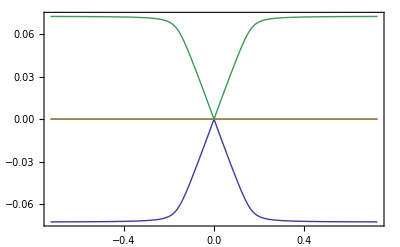

```mathematica
Plot[{EE[KX,t][[11]],EE[KX,t][[12]],EE[KX,t][[13]],EE[KX,t][[14]]},{t,-2Pi/Sqrt[3]/5,2Pi/Sqrt[3]/5},Frame->True]
```

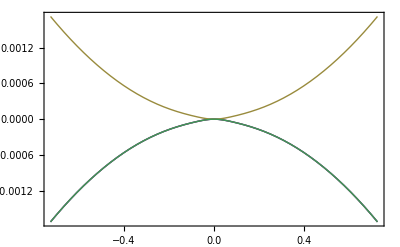

```mathematica
Plot[{EE[t,KX][[12]],EE[t,KX][[12]],EE[t,KX][[13]],EE[t,KX][[12]]},{t,-2Pi/Sqrt[3],2Pi/Sqrt[3]},Frame->True]
```

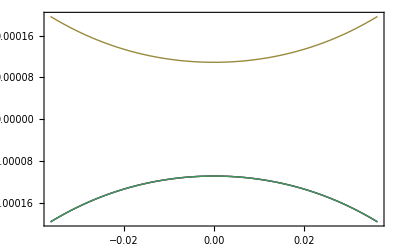

```mathematica
Plot[{EE[KX,t][[12]],EE[KX,t][[12]],EE[KX,t][[13]],EE[KX,t][[12]]},{t,-2Pi/Sqrt[3]/100,2Pi/Sqrt[3]/100},Frame->True]
```

```mathematica
Table[Plot[{EE[i/3,t][[11]],EE[i /3,t][[12]],EE[i/3,t][[13]],EE[i/3,t][[14]]},{t,-2Pi/Sqrt[3],2Pi/Sqrt[3]},Frame->True],{i,0,5}]
```